# Lab_Work_4

# 1

```mathematica
1. Что следует вписать вместо Yaaa для получения  показанного ниже графика?
```

```mathematica
(*ContourPlot - контурный график на плоскости, который показывает линии равного уровня(изолинии); контурные графики (или графики в горизонталях) наиболее часто используюются в топографии для представления на плоскости объёмного рельефа местности
PlotRangePadding - опция для графических функций,которая указывает,насколько другие оси и т.д.должны выходить за пределы диапазона координат,указанного в PlotRange.*)
(*Парметр PlotRangePadding->{{1,4}, {0,2}} для данного графика будет идентичен параметру PlotRange->{{14,-1}, {0,6}} и должен работать по такому принципу:
РАБОЧИЙ ПРИМЕР Graphics[{Pink,Rectangle[]},Frame->True,PlotRangePadding->{{1,4},{0,2}}]*)
```

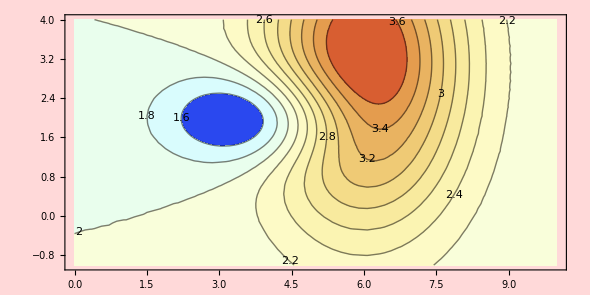

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat =(ymax-ymin)/(xmax-xmin);

fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2E^(-(x/2-3)^2-(y/3-1)^2);
grf2Db=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11, ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,(*Yaaa*)PlotRangePadding->{{1,4},{0,2}},  Background->LightRed]
```

```mathematica
2. Что следует вписать вместо Ybbb для получения  показанного ниже графика?
```

```mathematica
(*PlotRegion - это опция для графических функций,которая определяет,какую область конечной области отображения должен заполнять график. PlotRegion ->{{xmin,xmax},{ymin,ymax}}определяет область в масштабированных координатах,которую график должен заполнить в окончательной области отображения*)
```

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat =(ymax-ymin)/(xmax-xmin);

fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2*E^(-(x/2-3)^2-(y/3-1)^2);
grf2Dc=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11, ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,(*Ybbb*)PlotRegion->{{0.3,1}, {0,0.8}},  Background->LightRed]
```

-Graphics-

```mathematica
3. Что следует вписать вместо Yccc для получения  показанного ниже графика?
```

```mathematica
(*ContourShading->None отключает заливку площадит между изолиниями(оцвечивание контуров)*)
```

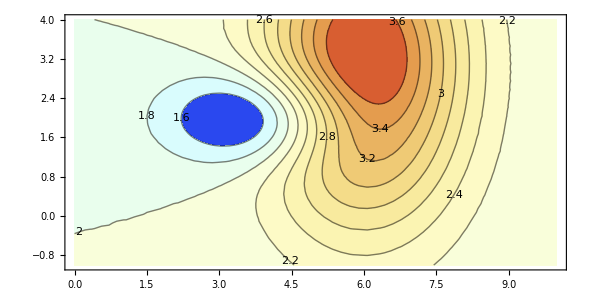

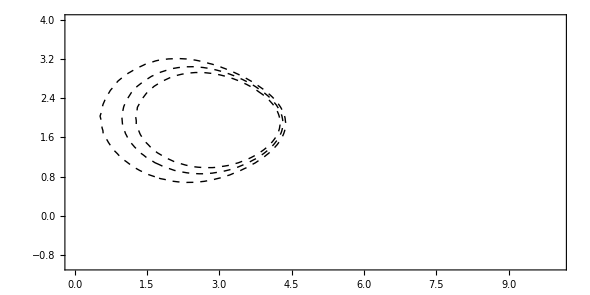

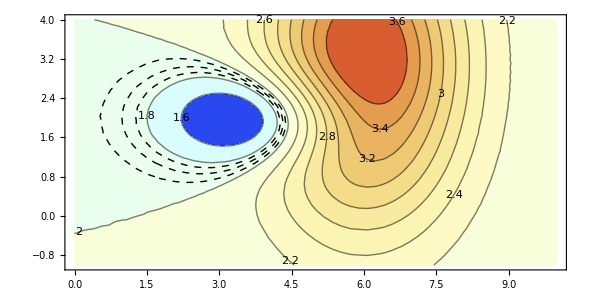

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat =(ymax-ymin)/(xmax-xmin);

fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2*E^(-(x/2-3)^2-(y/3-1)^2);
grf2D=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11, ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590]
grf2Dc=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->{1.85,1.9,1.95},ContourStyle->Dashed,(*Yccc*)ContourShading->None,AspectRatio->aspRat,ImageSize->590]
Show[grf2D, grf2Dc]
```

```mathematica
4. Что следует вписать вместо Yddd для получения  показанного ниже графика?
```

```mathematica
(*Inset - подставляет объект в графику
Scaled[{x,y}] - дает положение графического объекта в единицах координат,масштабируемых от 0 до 1 по всему диапазону графика в каждом направлении*)
```

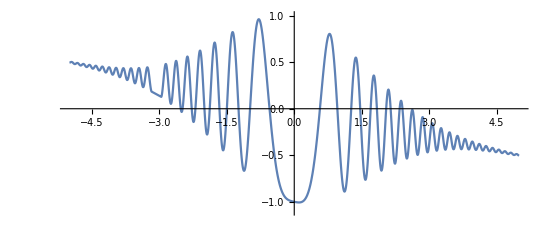

```mathematica
f3[x_] :=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
grf1DdFrgm=Plot[f3[x],{x,-4,-3},AspectRatio->3/7];
Plot[f3[x],{x,-5,5},AspectRatio->3/7,Epilog->(*Yddd*)Inset[grf1DdFrgm,Scaled[{0.05, .05}],Scaled[{0, 0}],4],PlotRange->{-1.1,1},PlotRangeClipping->False,ImageSize->550]
```

```mathematica
5. Что следует вписать вместо Yeee для получения  показанного ниже графика справа?
```

```mathematica
(*DensityPlot - плотностный график (карта зон), значение функции в каждой точке отображается при помощи окрашивания в определённый цвет, можно задавать интервалы и соответствующие им цвета, можно применять плавные уветовые переходы(градиентная заливка)
DensityPlot[f,{x,xmin,xmax},{y,ymin,ymax}] - строит график плотности f как фукнцию от x и y*)
```

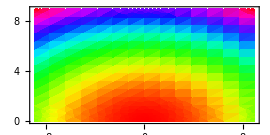
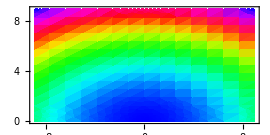

```mathematica
grf2Dd=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction->Hue,ImageSize->270];
grf2De=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction-> (*Yeee*)(Hue[2/3-#]&),ImageSize->270];

Row[{grf2Dd,grf2De},Spacer[5]]
```